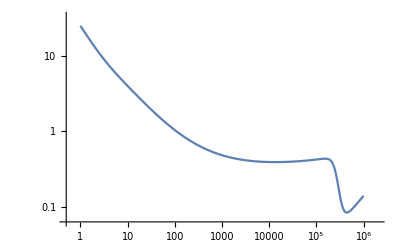

```mathematica
Cd[re_]:=24/re+(2.6*(re/5.0))/(1+(re/5.0)^1.52)+(.411*(re/263000)^-7.94)/(1+(re/263000)^-8)+(re^(.8)/461000)

LogLogPlot[Cd[re],{re,1,10^6}]
```